# Implicit Differentiation

## Don’t Forget the Chain Rule

The Chain Rule is the most important derivative rule. Be sure these examples make sense:

#### Example 1:

```mathematica
y=(x^3-7 x)^6
y'=6 (x^3-3 x)^5 (3 x^2-7)
```

To a friend, you might describe this as: “The derivative of (stuff)^6 is 6(stuff)^5·(derivative of stuff)

#### Example 2:

```mathematica
f(x)=sin(x^7)
f'(x)=cos(x^7)·(7 x^6)
```

To a friend, you might describe this as: “The derivative of sin(stuff) is cos(stuff)·(derivative of stuff)

#### Example 3:

```mathematica
h(x)=tan(stuff)
```

Describe the derivative of h(x) according the examples 1 & 2:

#### Example 4:

```mathematica
g(x)=(stuff)^2
```

Describe the derivative of g(x) according the examples 1 & 2:

## Implicitly Defined Functions

#### Explicit:

Functions defined explicitly are written as y=f(x). For example:

```mathematica
y=x^6-3 x^2+7
y=sin^2(x)-7 cos(x)
y=(2x-3)/(x+6)
```

y is isolated on the left and x is the only variable on the right side of the equal sign.

#### Implicit

Relations defined implicitly are usually not functions and are not “solved for y.” For example:

```mathematica
x^2+y^2==25
x=y^2
2y=x^2+5sin(y)
3 y^2-2 x^3+6y+24x=0
```

Here are graphs of these four implicit relations (not functions!):

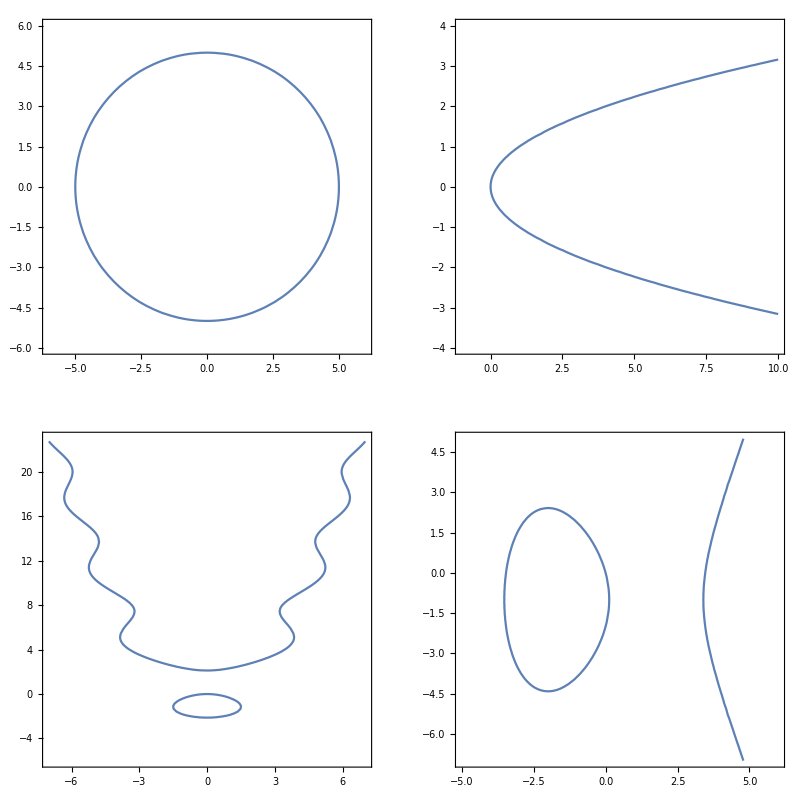

```mathematica
GraphicsGrid[
{{ContourPlot[x^2+y^2==25,{x,-6,6},{y,-6,6}],
ContourPlot[x==y^2,{x,-1,10},{y,-4,4}]},{
ContourPlot[2y==x^2+5Sin[y],{x,-7,7},{y,-6,23}],
ContourPlot[3 y^2-2 x^3+6y+24x==0,{x,-5,6},{y,-7,5}]
}}
]
```

### Derivatives of Implicit Relations

In order to find the derivative implicitly, we need to remember that while we cannot explicitly solve for y as a function of x, that y does represent some function of x, we just cannot solve for it.
So we can think of this as:

The derivative of y is ⅆy/ⅆx.
Using the Chain Rule, the derivative of (stuff)^4 is 4(stuff)^3·(derivative of stuff).
Putting these together, using “y” as the “stuff”:
The derivative of (y)^4 is 4(y)^3·ⅆy/ⅆx

### Example 5

Start with an implicitly defined relation. Here is the equation of a circle:

x^2+y^2=25

Now take the derivative of each side with respect to x, term by term. Notice the chain rule is needed on the y^2 term:

2x+2y ⅆy/ⅆx=0

Now solve for ⅆy/ⅆx with algebra:

2y ⅆy/ⅆx=-2x
ⅆy/ⅆx=-(2x)/(2y)
ⅆy/ⅆx=-x/y

Here is the Mathematica solution:

```mathematica
Solve[D[x^2+y[x]^2==25,x],y'[x]]/.y[x]->y
```

{{y'(x)→-x/y}}

#### Practice 5:

Find ⅆy/ⅆx for x=y^2 (by hand):

You can check your answer with the following input cell. 
Click in the cell and press [shift] [enter]:

```mathematica
Solve[D[x==y[x]^2,x],y'[x]]/.y[x]->y
```

### Example 6

Normal derivative rules apply...this example uses the product rule. Start with:

x^2-x y+y^2=7

Now take the derivative of each side, term by term. Notice the product rule is needed on the x·y term, and the subtraction needs to be distributed:

2x-(x ⅆy/ⅆx+y·(1))+2y·ⅆy/ⅆx=0

Now solve for ⅆy/ⅆx with algebra:

2x-x ⅆy/ⅆx-y+2y·ⅆy/ⅆx=0
-x ⅆy/ⅆx+2y·ⅆy/ⅆx=y-2x
ⅆy/ⅆx(-x+2y)=y-2x
ⅆy/ⅆx=(y-2x)/(-x+2y)
ⅆy/ⅆx=(y-2x)/(2y-x)

Mathematica gets the same result. Notice that while the fraction looks slightly different (x comes before y), it is equivalent to our answer. This could happen in a multiple-choice question!

```mathematica
Solve[D[x^2-x y[x]+y[x]^2==7,x],y'[x]]/.y[x]->y
```

{{y'(x)→(2 x-y)/(x-2 y)}}

It is very common to have several ⅆy/ⅆx terms after taking the derivative implicitly.

#### Practice 6:

Find ⅆy/ⅆx for 2y=x^2+5sin(y)  (by hand):

You can check your answer with the following input cell. Click inside and press [shift] [enter]:

```mathematica
Solve[D[2y[x]==x^2+5Sin[y[x]],x],y'[x]]/.y[x]->y
```

### Example 7

Find the equations for the horizontal and vertical tangent lines for:

3 y^2-2 x^3+6y+24x=0

Horizontal tangent lines have a slope of zero, so we will find these by setting ⅆy/ⅆx=0 and solving.
Vertical tangent lines have undefined slope, so we will look where ⅆy/ⅆx is undefined.
For both, the starting point is finding ⅆy/ⅆx.

Now take the derivative of each side of 3 y^2-2 x^3+6y+24x=0, term by term...Don’t forget the Chain Rule for terms with y!

6y·ⅆy/ⅆx-6 x^2+6 ⅆy/ⅆx+24=0

Done with calculus, now solve for ⅆy/ⅆx with algebra:

6y·ⅆy/ⅆx+6 ⅆy/ⅆx=6 x^2-24
ⅆy/ⅆx(6y+6)=6 x^2-24
ⅆy/ⅆx=(6 x^2-24)/(6y+6)
ⅆy/ⅆx=(x^2-4)/(y+1)

To find the horizontal tangent lines, set ⅆy/ⅆx=0 and solve:

(x^2-4)/(y+1)=0
x^2-4=0   A fraction is zero when the numerator is zero
x^2=4
x=±2

We have two answers...but horizontal line equations look lik y=constant, so we need to substitute each answer into the original equation to find the corresponding y-value:

3 y^2-2(-2)^3+6y+24(-2)=0   ⇒  y=-4.416 or y=2.416

3 y^2-2(2)^3+6y+24(2)=0  ⇒  no solution (imaginary)

The horizontal tangent lines are y=-4.416 and y=2.416

For the vertical tangent lines, ⅆy/ⅆx=(x^2-4)/(y+1) is undefined. A fraction is undefined when the denominator is zero:

y+1=0
y=-1

We have a similar problem...vertical lines have an equation in the form x=constant, so we need to substitute y=-1 into the original equation to solve for x:

3(-1)^2-2 x^3+6(-1)+24x=0    ⇒  x=-3.638, x=0.380, or x=3.259

The vertical tangent lines are x=-3.638, x=0.380, and x=3.259

Can you see where these five tangent lines (2 horizontal and 3 vertical) are on the graph?

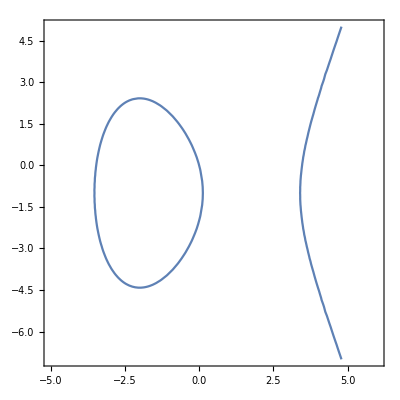

```mathematica
ContourPlot[3 y^2-2 x^3+6y+24x==0,{x,-5,6},{y,-7,5}]
```

#### Practice 7

What are the steps to find the equations of horizontal tangent lines?

#### Practice 8

What are the steps to find the equations of vertical tangent lines?

## Authorship Information

Dan Uhlman
uhlmand@tas.tw